```mathematica
(*2. Считать данные из полученного входного файла в системе Wolfram Mathematica (учесть, что размерность графа может быть любой и параметры bi могут идти в произвольном порядке).*)
```

```mathematica
inFileName=StringJoin[NotebookDirectory[],"input.txt"];
fileStream=OpenRead[inFileName];
Is=Read[fileStream,{Word,Number}][[2]];
Us=Read[fileStream,{Word,Number}][[2]];
U=ReadList[fileStream,Expression,Us];
b=ReadList[fileStream,String,Is];
Close[fileStream];
b=Sort[Table[StringSplit[b[[i]],{"b","_","/*","*/ ", " "}], {i,Is}]];
UDirect=Table[U[[i,1]]->U[[i,2]],{i,Us}];
```

```mathematica
g=Graph[UDirect, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick];
```

```mathematica
(*3. Построить списковые структуры хранения корневого дерева (список узлов, список предков, список направлений, список глубин узлов, список связи или династического обхода;корень дерева-узел, от которого строили покрывающее дерево, либо любой произвольный узел.*)
pred=ConstantArray[0,Is];(*список предков*)
dir=ConstantArray[0,Is];(*список направлений*)
depth=ConstantArray[0,Is]; (*список глубин узлов*)
dinast=ConstantArray[0,Is];(*династичесий обход*)
posl={};                                            (*последовательность обхода*)
RootTree={};                                   (*корневое дерево*)
Ut={};                                               (*покрывающее дерево*)
root=1;
ug=UndirectedGraph[g];
DepthFirstScan[ug,root,{"FrontierEdge"->Function[edge,{
pred[[edge[[2]]]]=edge[[1]],
depth[[edge[[2]]]]=depth[[edge[[1]]]] + 1,
{i=edge[[1]]->edge[[2]],AppendTo[RootTree,i],If[MemberQ[UDirect,i],{AppendTo[Ut,i],dir[[edge[[2]]]]=1},{AppendTo[Ut,edge[[2]]->edge[[1]]],dir[[edge[[2]]]]=-1}]}
}],
"PrevisitVertex"->Function[vertex,{If[posl≠{},dinast[[posl[[-1]]]]=vertex],AppendTo[posl,vertex]}]
}];
dinast[[posl[[-1]]]]=root;
(*Print[Range[Is]];
Print[pred];
Print[depth];
Print[dir];
Print[dinast];
Print[posl];*)
```

## Лабораторная 6.

```mathematica
(* 1. Реализовать функцию нахождения компонент характеристических векторов (в функциональном стиле).*)
Un=Complement[UDirect,Ut];
edges=Subscript[x,#]&/@Join[Un,Ut];
c[{k_,l_}]:=Return[{pred[[k]],l}]/;depth[[k]]>depth[[l]];
c[{k_,l_}]:=Return[{k,pred[[l]]}]/;depth[[k]]<depth[[l]];
c[{k_,l_}]:=Return[{pred[[k]],pred[[l]]}]/;depth[[k]]==depth[[l]];
DefineCycle[arc_]:=NestWhileList[c,arc,First[##]≠Last[##]&];
delta[e_]:=Block[{result},
result=#->0&/@edges;
cycle=DefineCycle[{e[[2]],e[[1]]}];
cycle=Transpose[cycle];
cycle=DeleteDuplicates[Flatten[Join[cycle[[1]],Reverse[cycle[[2]]]]]];
cycle=Table[cycle[[i]]->cycle[[i+1]],{i,1,Length[cycle]-1}];
AppendTo[cycle,e];

r[x_]:=0;
r[x_]:=1/;MemberQ[cycle,x[[2]]];
r[x_]:=-1/;MemberQ[cycle,x[[2]][[2]]->x[[2]][[1]]];
result=#->r[#]&/@edges;
Return[result];
]
```

Покрывающее дерево графа с циклами, порождёнными дугами множества Un:

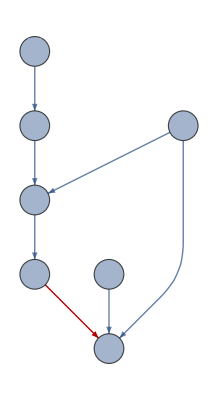
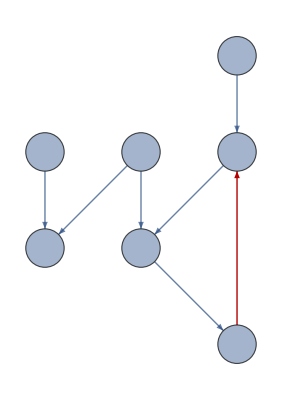
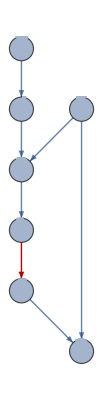
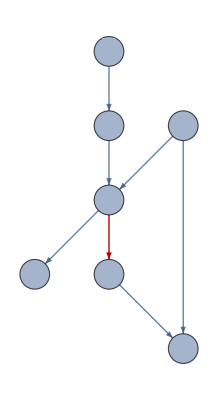
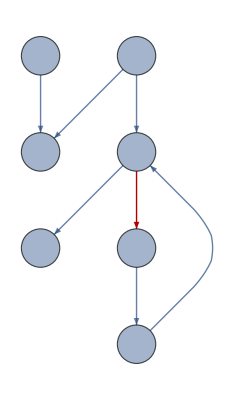
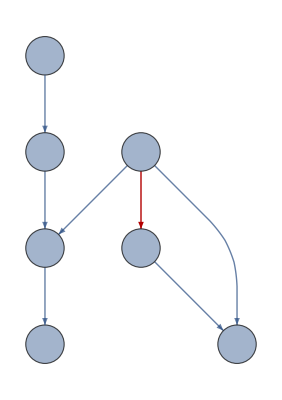
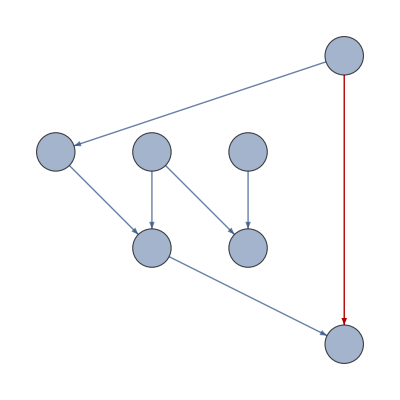

```mathematica
(* 2. Вывести покрывающее дерево графа с циклами, порождёнными дугами множества Un (см.пример).*)
CellPrint[TextCell["Покрывающее дерево графа с циклами, порождёнными дугами множества Un:","Output"]];
img=Table[Graph[Append[Ut,i],GraphHighlight->i,GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4,VertexLabelStyle-> Directive[Italic, 28]],{i,Un}]
(*NotebookWrite[nb2,ToBoxes[img]];*)
(*SelectionCreateCell[EvaluationNotebook[],nb2];*)
(*SelectionMove[EvaluationNotebook[],All,GeneratedCell];*)
NotebookWrite[nb2,"Output"];
```

```mathematica
(* 3. Вычислить характеристические векторы, порождённые дугами множества Un. Компоненты векторов вывести в виде таблицы (см.пример).*)
CellPrint[TextCell["Характеристические векторы, порождённые дугами множества Un:","Output"]];
answer=Table[delta[i],{i,Un}]
data=Table[Prepend[Table[i[[2]],{i,answer[[j]]}],Un[[j]]],{j,1,Length[Un]}];
Grid[Prepend[data,Prepend[edges," "]],Dividers->{{2->Thick},{2->Thick}}]
(*SelectionMove[nb2,Next,Cell];*)
NotebookFind[EvaluationNotebook[],"Output",All,CellStyle];
```

Характеристические векторы, порождённые дугами множества Un:

{{x_(1->2)→1,x_(1->4)→0,x_(1->6)→0,x_(3->6)→0,x_(3->7)→0,x_(5->6)→0,x_(7->1)→0,x_(3->1)→1,x_(4->3)→0,x_(7->4)→0,x_(5->3)→1,x_(5->2)→-1,x_(6->2)→0},{x_(1->2)→0,x_(1->4)→1,x_(1->6)→0,x_(3->6)→0,x_(3->7)→0,x_(5->6)→0,x_(7->1)→0,x_(3->1)→1,x_(4->3)→1,x_(7->4)→0,x_(5->3)→0,x_(5->2)→0,x_(6->2)→0},{x_(1->2)→0,x_(1->4)→0,x_(1->6)→1,x_(3->6)→0,x_(3->7)→0,x_(5->6)→0,x_(7->1)→0,x_(3->1)→1,x_(4->3)→0,x_(7->4)→0,x_(5->3)→1,x_(5->2)→-1,x_(6->2)→1},{x_(1->2)→0,x_(1->4)→0,x_(1->6)→0,x_(3->6)→1,x_(3->7)→0,x_(5->6)→0,x_(7->1)→0,x_(3->1)→0,x_(4->3)→0,x_(7->4)→0,x_(5->3)→1,x_(5->2)→-1,x_(6->2)→1},{x_(1->2)→0,x_(1->4)→0,x_(1->6)→0,x_(3->6)→0,x_(3->7)→1,x_(5->6)→0,x_(7->1)→0,x_(3->1)→0,x_(4->3)→1,x_(7->4)→1,x_(5->3)→0,x_(5->2)→0,x_(6->2)→0},{x_(1->2)→0,x_(1->4)→0,x_(1->6)→0,x_(3->6)→0,x_(3->7)→0,x_(5->6)→1,x_(7->1)→0,x_(3->1)→0,x_(4->3)→0,x_(7->4)→0,x_(5->3)→0,x_(5->2)→-1,x_(6->2)→1},{x_(1->2)→0,x_(1->4)→0,x_(1->6)→0,x_(3->6)→0,x_(3->7)→0,x_(5->6)→0,x_(7->1)→1,x_(3->1)→-1,x_(4->3)→-1,x_(7->4)→-1,x_(5->3)→0,x_(5->2)→0,x_(6->2)→0}}

| x_(1->2) | x_(1->4) | x_(1->6) | x_(3->6) | x_(3->7) | x_(5->6) | x_(7->1) | x_(3->1) | x_(4->3) | x_(7->4) | x_(5->3) | x_(5->2) | x_(6->2)
1->2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 0
1->4 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
1->6 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | -1 | 1
3->6 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1
3->7 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
5->6 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 1
7->1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 0 | 0 | 0